```mathematica
path = FileNameJoin[Drop[#,Flatten@{Position[#,"Master"]+1,-1}]&@StringSplit[NotebookDirectory[],"\\"]];
```

## 24 Апереля, параллельное падение пучков.

```mathematica
ClearAll[data24,wForm24April]
data24=Table[Import[path<>"\\Data\\2015\\April\\24\\24apr_"<>ToString[i]<>"ac.dat"],{i,1,7}];
wForm24April=Import[path<>"\\Data\\2015\\April\\24\\24apr_1.dat"];
```

## Волновая форма меза1200/100.

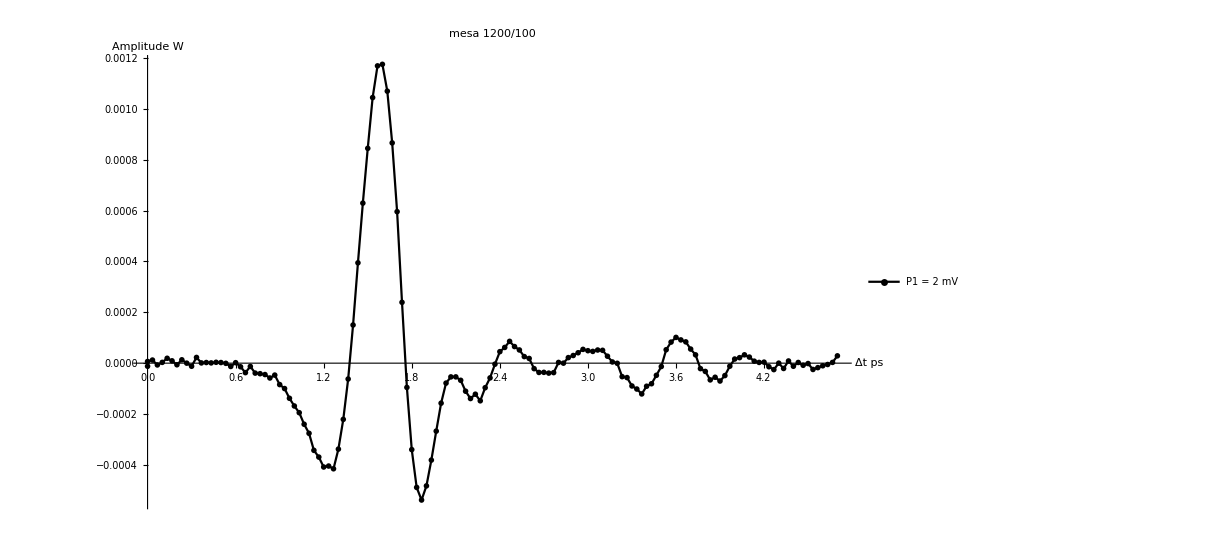

```mathematica
ListLinePlot[wForm24April[[All,{3,2}]],PlotLegends->{"P1 = 2 mV"},ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->All]
```

## Динамика.

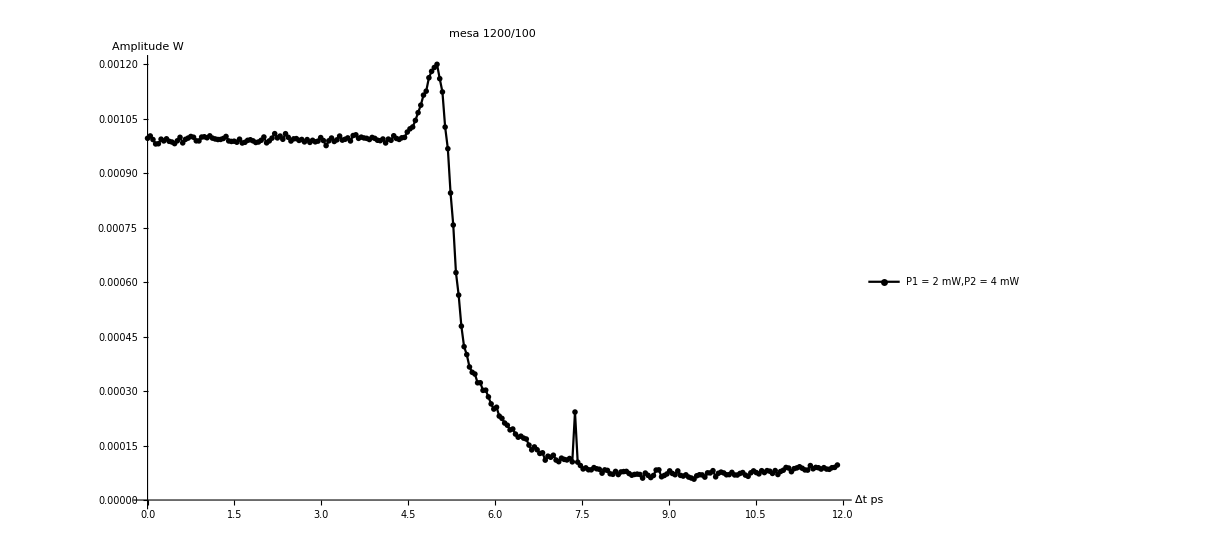

```mathematica
ListLinePlot[data24[[2]][[All,{3,2}]],PlotLegends->{"P1 = 2 mW,P2 = 4 mW"},ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->All]
```

## Зависимость волн.ф-мы от типа поляризации.

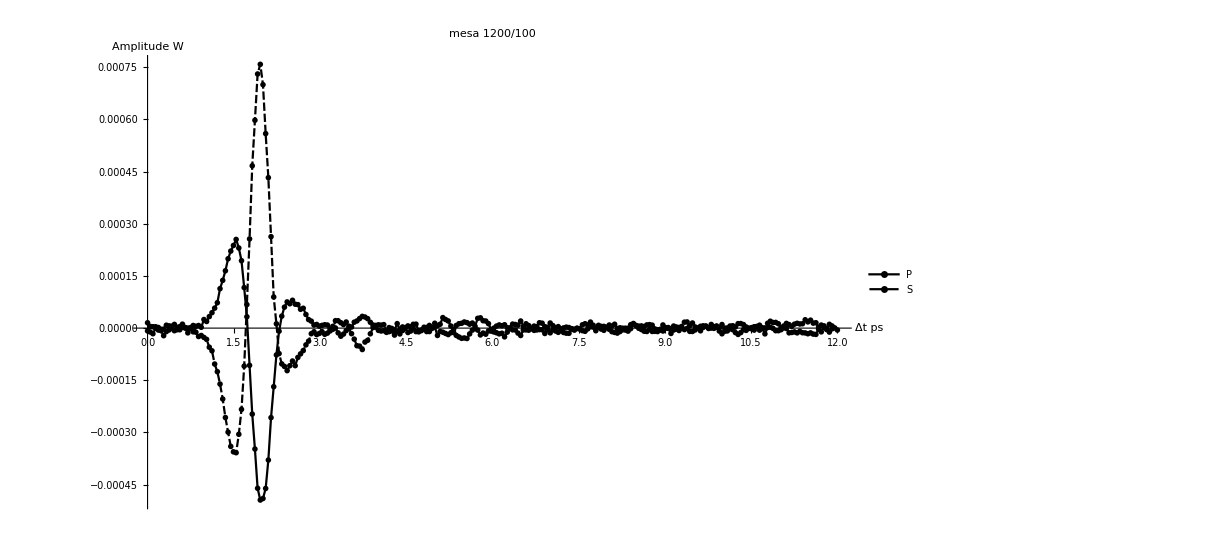

```mathematica
ListLinePlot[Table[data24[[i]][[All,{3,2}]],{i,{3,6}}],PlotLegends->{"P","S"},ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->All]
```

## 26 Апреля, второй пучок падает перпендикулярно плоскости образца.

```mathematica
ClearAll[data26,wForm26April1,wForm26April2,wForm26April3]
data26=Table[Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2015\\April\\26\\26apr_"<>ToString[i]<>"ac.dat"],{i,1,16}];
wForm26April1=Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2015\\April\\26\\26apr_1.dat"];
wForm26April2=Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2015\\April\\26\\26apr_2.dat"];
wForm26April3=Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2015\\April\\26\\26apr_3.dat"];
```

## Волновые формы при разных мощьностях P1.

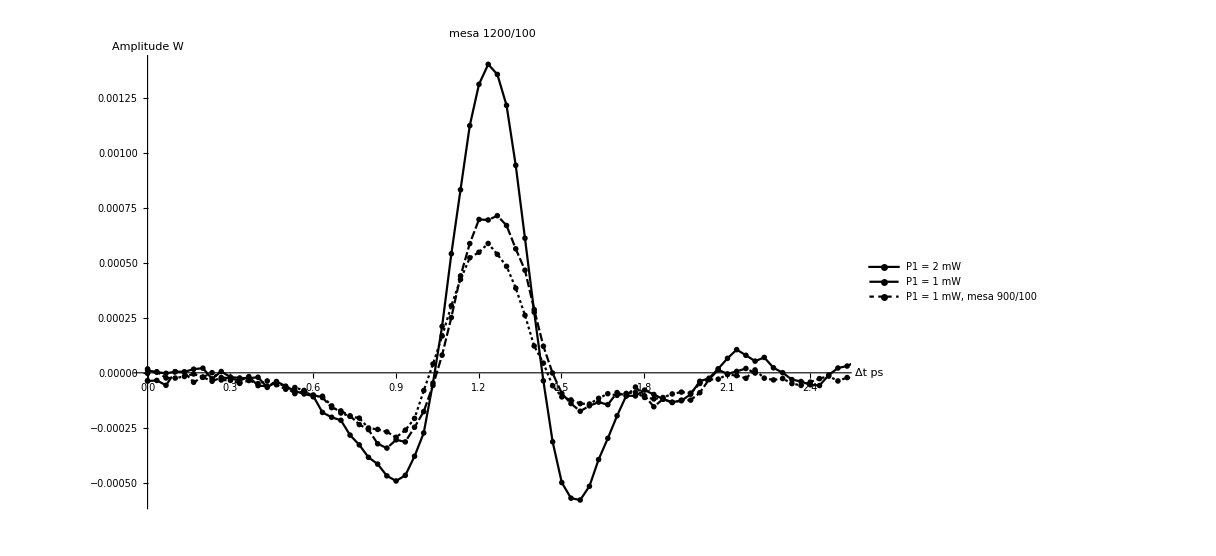

```mathematica
ListLinePlot[{wForm26April1[[All,{3,2}]],wForm26April2[[All,{3,2}]],wForm26April3[[All,{3,2}]]},PlotLegends->{"P1 = 2 mW","P1 = 1 mW","P1 = 1 mW, mesa 900/100"},ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->{{0,2.5},All}]
```

## Динамика, меза 1200/100

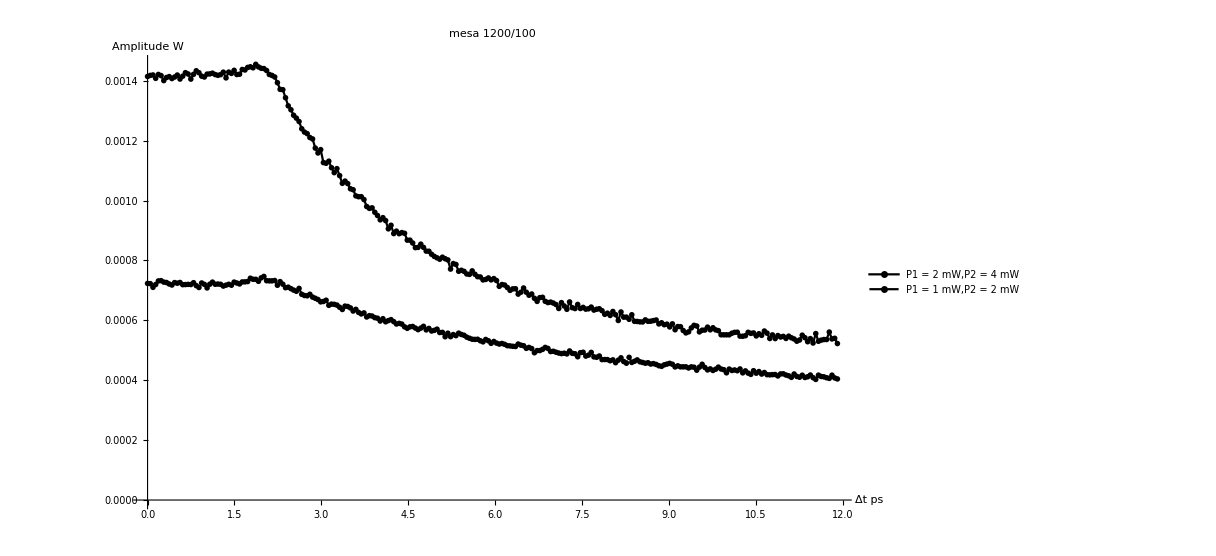

```mathematica
ListLinePlot[{data26[[3]][[All,{3,2}]],data26[[5]][[All,{3,2}]]},PlotLegends->{"P1 = 2 mW,P2 = 4 mW","P1 = 1 mW,P2 = 2 mW"},ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->All]
```

## Динамика, меза 1200/100 мощность P1 = 1 mW.

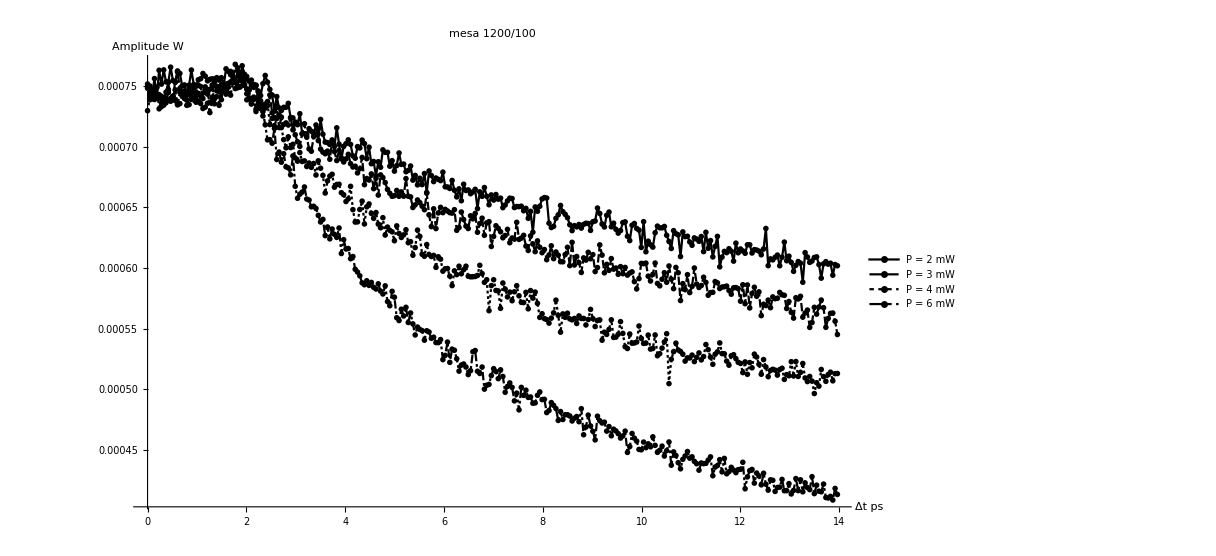

```mathematica
ListLinePlot[Table[data26[[i]][[All,{3,2}]],{i,9,12}],PlotLegends->{"P = 2 mW","P = 3 mW","P = 4 mW","P = 6 mW"},ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->All]
```

## Меза 1500/100

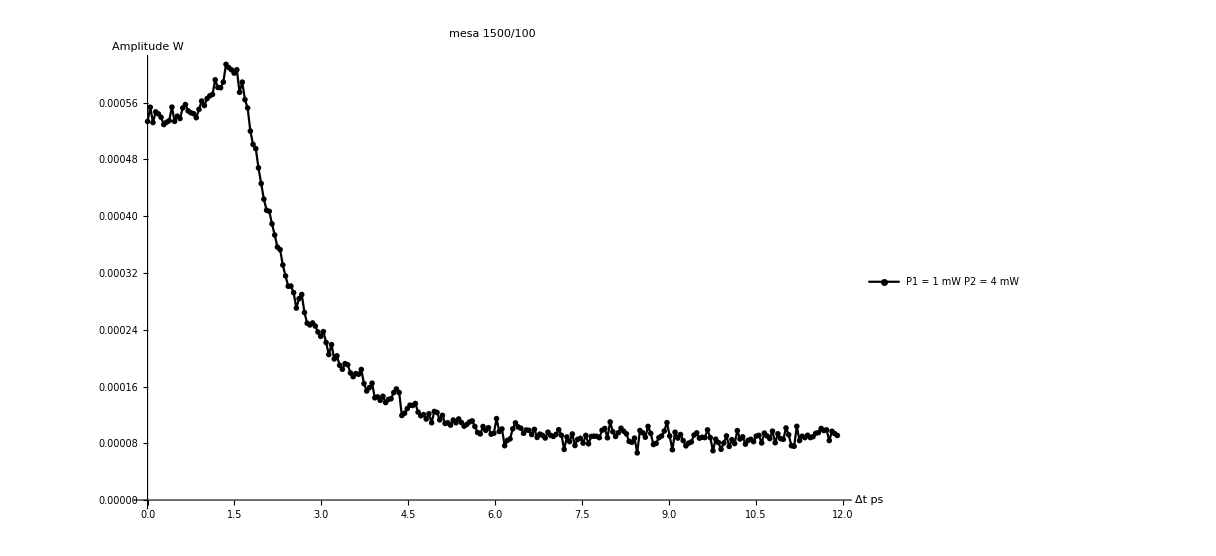

```mathematica
ListLinePlot[data26[[15]][[All,{3,2}]],PlotLegends->{"P1 = 1 mW P2 = 4 mW"},ImageSize->900,PlotLabel->"mesa 1500/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->All]
```

## 27 Апреля.

```mathematica
ClearAll[data27,wForm27April1,wForm27April2]
data27=Table[Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2015\\April\\27\\27apr_"<>ToString[i]<>"ac.dat"],{i,1,14}];
wForm27April1=Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2015\\April\\27\\27apr_1.dat"];
wForm27April2=Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2015\\April\\27\\27apr_2.dat"];
```

## Волновые формы меза 1200/100 и InAs

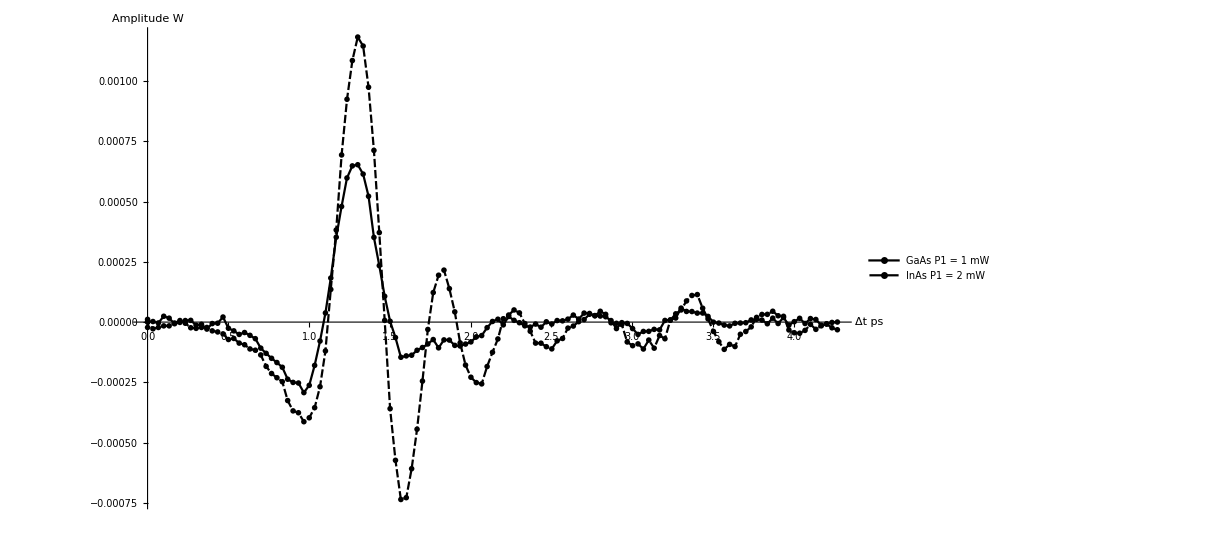

```mathematica
ListLinePlot[{wForm27April1[[All,{3,2}]],wForm27April2[[All,{3,2}]]},PlotLegends->{"GaAs P1 = 1 mW","InAs P1 = 2 mW"},ImageSize->900,AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->All]
```

## Динамика, меза 1200/100

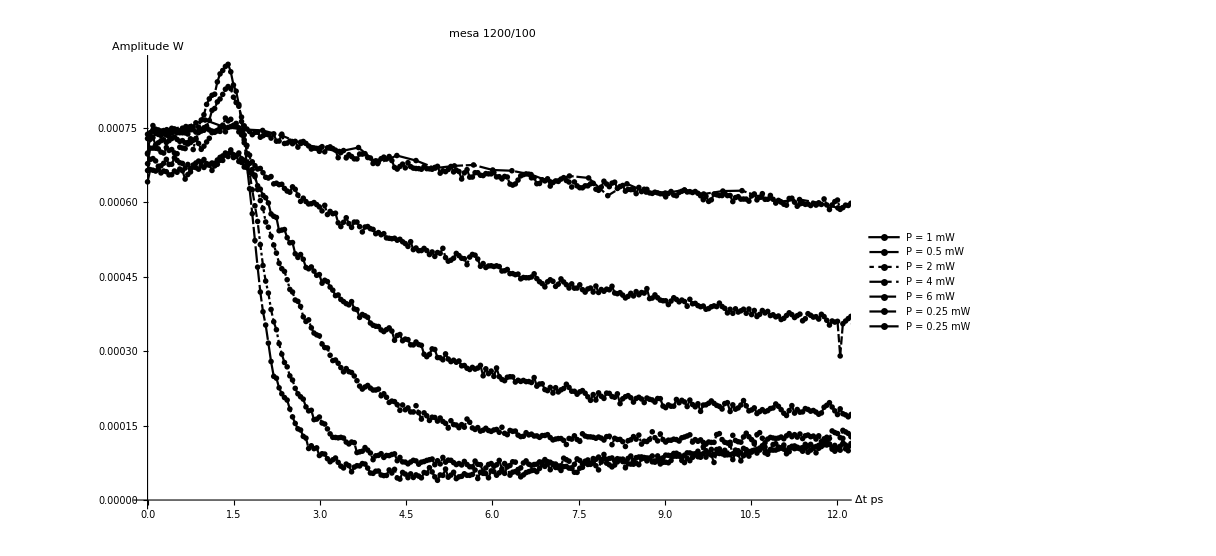

```mathematica
ListLinePlot[Table[data27[[i]][[All,{3,2}]],{i,1,7}],PlotLegends->{"P = 1 mW","P = 0.5 mW","P = 2 mW","P = 4 mW","P = 6 mW","P = 0.25 mW","P = 0.25 mW"},ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->{{0,12},All}]
```

## Динамика при P1=2 mW.

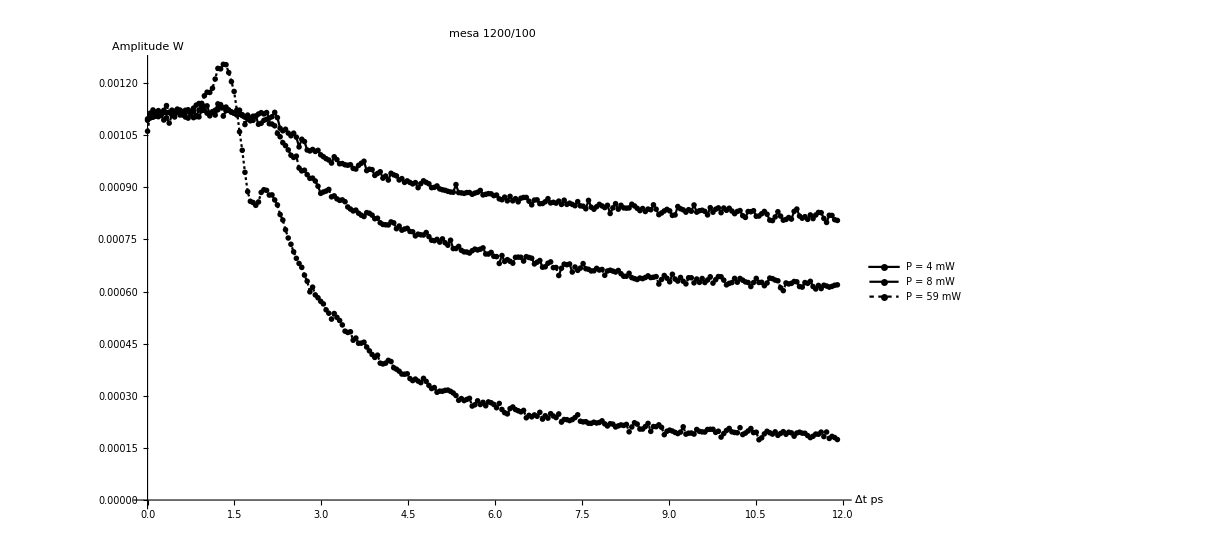

```mathematica
ListLinePlot[Table[data27[[i]][[All,{3,2}]],{i,9,11}],PlotLegends->{"P = 4 mW","P = 8 mW","P = 59 mW"},ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->All]
```

## 29 Апреля.

```mathematica
ClearAll[data29]
data29=Table[Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2015\\April\\29\\29apr_"<>ToString[i]<>"ac.dat"],{i,1,18}];
```

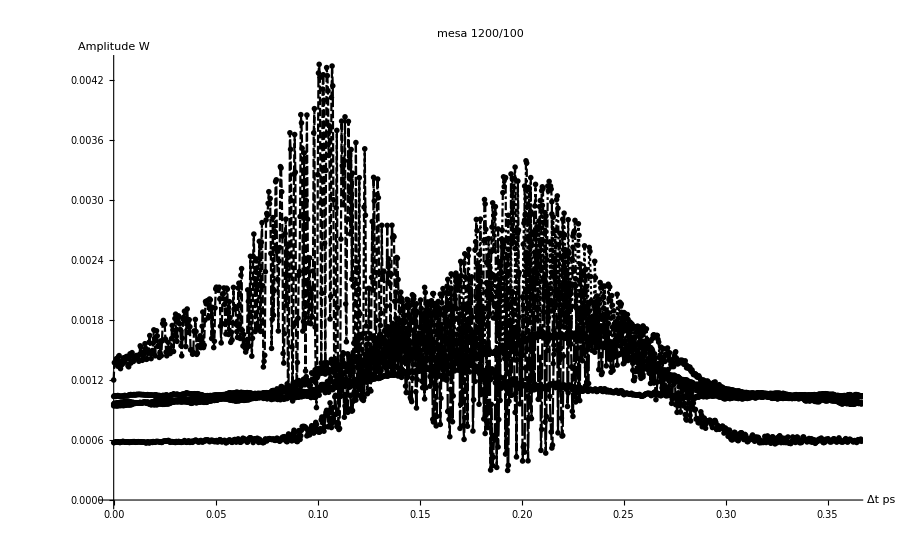

```mathematica
ListLinePlot[Table[data29[[i]][[All,{3,2}]],{i,2,6}],ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->{{0,0.36},All}]
```

## Без фильтров

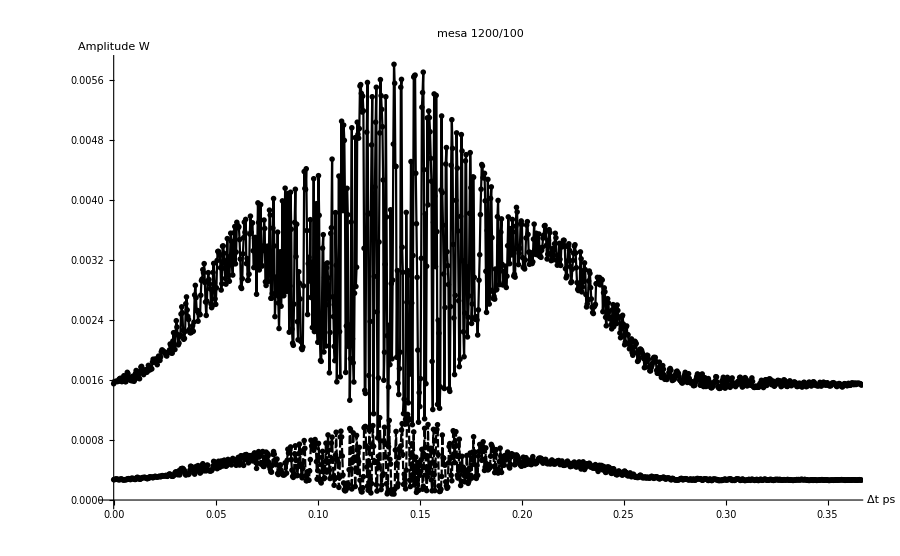

```mathematica
ListLinePlot[Table[data29[[i]][[All,{3,2}]],{i,8,9}],ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->{{0,0.36},All}]
```

## Без λ/2

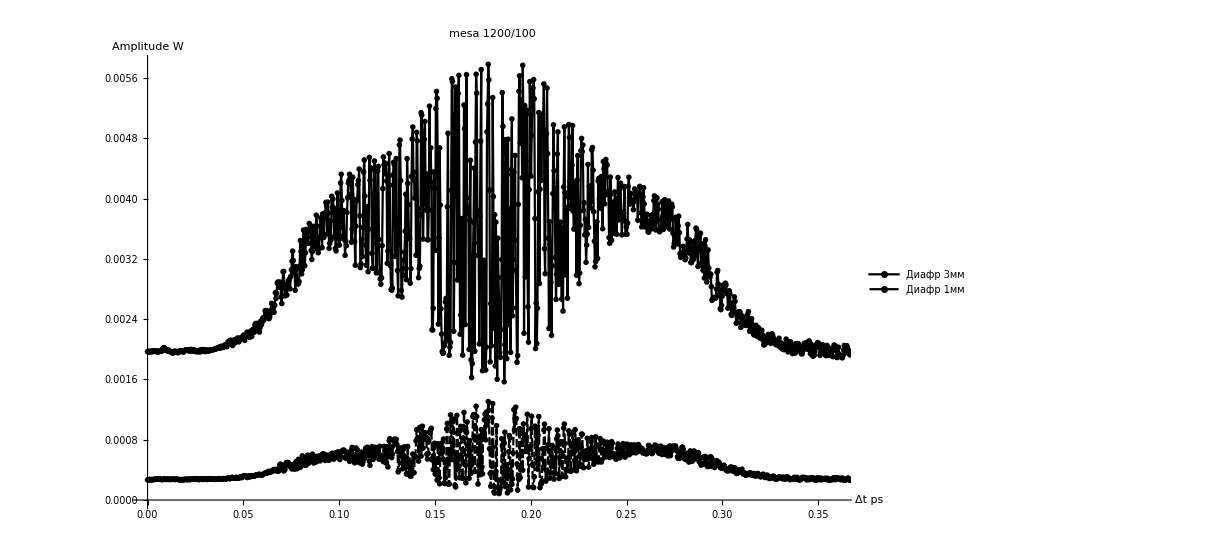

```mathematica
ListLinePlot[Table[data29[[i]][[All,{3,2}]],{i,14,15}],ImageSize->900,PlotLabel->"mesa 1200/100",AxesLabel->{"Δt ps","Amplitude W"},LabelStyle->18,PlotRange->{{0,0.36},All},PlotLegends->{"Диафр 3мм","Диафр 1мм"}]
```